```mathematica
Datos
```

```mathematica
Eta0mvsr={{16.428125000000097,0.39714481578951344},{13.06718750000005,0.46085808011362384},{11.109375000000023,0.5063347178250697},{8.747656249999988,0.5623289322006965},{7.317187499999982,0.5900277824993562},{7.092968749999984,0.5932670639204777},{6.883593749999984,0.5958845229279883},{6.687499999999985,0.5979418236777415},{6.503906249999985,0.5994755073315254},{6.331249999999986,0.6005303047055819},{6.168749999999986,0.6011441223749877},{6.014843749999987,0.6013503537712537},{5.869531249999987,0.601179964067311},{5.731249999999988,0.6006603636239376},{5.599999999999988,0.5998171303507368},{5.03124999999999,0.5915175577819682},{4.574999999999992,0.5779928930248511},{4.201562499999993,0.5608565383461382},{3.8898437499999945,0.5412562569718621},{2.9539062499999975,0.43033234903740786}};

Etam03mvsr={{13.181250000000052,0.4964645288431268},{11.450000000000028,0.5630646947164795},{8.942968749999991,0.6469557671702563},{7.479687499999982,0.7033465994327796},{7.194531249999983,0.7094223876546102},{6.998437499999984,0.7178890470570014},{6.810546874999983,0.7254078082909935},{6.567578124999985,0.7291475161919412},{6.418749999999985,0.7361201722015234},{6.2453124999999865,0.7408711007888703},{6.096484374999987,0.7457905294710554},{5.955859374999987,0.7501155137883715},{5.795312499999988,0.7526562328787086},{5.645703124999988,0.7548569369684418},{5.02460937499999,0.7610845967449962},{4.492187499999993,0.7565900326931241},{4.044921874999994,0.7450241995126884}};

Etam05mvsr={{13.301562500000054,0.5203227129883475},{11.684375000000031,0.5976558351378544},{9.028124999999994,0.6994818421626545},{7.537499999999982,0.7711362892600483},{7.313671874999982,0.7832117296240112},{7.069140624999982,0.7924039619948524},{6.8570312499999835,0.8016161095178862},{6.653906249999984,0.8098496584347504},{6.475781249999986,0.8180939925158035},{6.305078124999985,0.8254712357771131},{6.183203124999986,0.8340605145380079},{5.974999999999987,0.8373480286711372},{5.857031249999987,0.8444727874212496},{5.673437499999988,0.8465379782397331},{5.027343749999991,0.8601382677234005},{4.91601562499999,0.861933838363771},{4.792187499999992,0.8617381204939468},{4.450390624999992,0.8593704393769762},{3.915624999999994,0.8470628428032237}};

Etam07mvsr={{13.170312500000051,0.5386994886917824},{11.525000000000029,0.6260379967362303},{9.169531249999993,0.7518479127281834},{7.570312499999981,0.835744957069066},{7.347656249999982,0.850562322889737},{7.1304687499999835,0.8638469336852674},{6.916406249999984,0.8755818789809235},{6.715624999999984,0.8865116857937958},{6.5238281249999845,0.8963781559168644},{6.344140624999985,0.9055592247909908},{6.171874999999986,0.9138345607328985},{6.0050781249999865,0.921177372904477},{5.845703124999988,0.9277592748962337},{5.692968749999989,0.9335905880918454},{4.999218749999991,0.9519564625084047},{4.699609374999992,0.9567617477870934},{4.3812499999999925,0.9541026679223336},{3.7749999999999946,0.9413204654746601}};

Etam095mvsr={{13.521875000000056,0.5720663769126121},{11.63906250000003,0.6662890727092202},{9.141406249999994,0.8106440441776203},{7.635546874999981,0.9153321124347772},{7.421874999999981,0.9343413109492453},{7.217968749999983,0.9518288190537347},{6.965234374999984,0.964365858572945},{6.763671874999984,0.9782832445547355},{6.580078124999985,0.9916600647956062},{6.380859374999986,1.0022934389289517},{6.200781249999986,1.0126858132050058},{6.026171874999987,1.021916831805621},{5.862890624999987,1.0306109038968319},{5.726953124999988,1.040375478107856},{4.95527343749999,1.0614462763698602},{4.612695312499992,1.0660759606745096},{4.271093749999993,1.0644043060701514},{3.5890624999999954,1.0567102592819406}};

mvsrBHm12={{12.481250000000042,0.562286269063265},{11.801562500000033,0.7080685491256471},{9.084765624999994,0.862558933224307},{7.332421874999982,0.9621098153391672},{6.287499999999986,1.050934841158064},{5.591015624999988,1.1316217361916177},{4.901953124999991,1.1689364243122868},{4.051562499999994,1.156784835469123}};
```

```mathematica
{Plot[{Interpolation[Eta0mvsr,InterpolationOrder->2][r]},{r,5,13},PlotRange->Full],Plot[{Interpolation[Etam03mvsr,InterpolationOrder->2][r]},{r,3.5,13}],Plot[{Interpolation[Etam05mvsr,InterpolationOrder->2][r]},{r,3.5,13}], Plot[{Interpolation[Etam07mvsr,InterpolationOrder->2][r]},{r,3.5,13}], Plot[{Interpolation[Etam095mvsr,InterpolationOrder->2][r]},{r,3.5,13}]}
```

```mathematica
(*Compacticidad*)
```

```mathematica
(*
 m=0; masa=Interpolation[Etam07mvsr,InterpolationOrder->2];
For[i=3.5, i<13+1,i+=0.001,
Mmax=masa[i];
If[m<Mmax,m=Mmax; posit=i]
]
(*Máxima compacticidad estable *)
CompMax=masa[posit]/posit;
CompMax2=m/posit
Print[CompMax]
*)
```

```mathematica
(*
compM=0;a=mvsrBS;
For[i=1, i<Length[a]+1,i++,
comp=a[[i,2]]/a[[i,1]];
If[comp>compM,compM=comp]
]
(*Máxima compacticidad *)
Print[compM]
*)
```

```mathematica
datos={Eta0mvsr,Etam03mvsr,Etam05mvsr,Etam07mvsr,Etam095mvsr, mvsrBHm12};
Compac={};
```

```mathematica
For[j=1,j<Length[datos]+1,j++,
     m=0; 
     masa=Interpolation[datos[[j]],InterpolationOrder->2];
(* Buscando el menor y mayor radio para empezar a buscar la masa maxima *)
    radio={};
    For[k=1,k< Length[datos[[j]]]+1,k++,
	a=datos[[j,k,1]]; 
	AppendTo[radio,a]];
   (*  Clear[ii,iii]; *)
    a=TakeSmallest[radio,1];
    b=TakeLargest[radio,1];
(*Print[ii];
Print[iii];
*)
(* Buscando la mayor masa *)
    For[i=a[[1]], i<b[[1]],i+=0.001,
	Mmax=masa[i];
	If[m<Mmax,m=Mmax; posit=i]
	];
(* Máxima compacticidad estable *)
CompMax=masa[posit]/posit;
CompMax2=m/posit; (*Comprobacion*)
Print[CompMax];
AppendTo[Compac,CompMax];
]
```

0.10011

0.152344

0.177225

0.205957

0.235216

0.252729

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*Resultado*)
```

```mathematica
errorCompac={{0,0.10010993357966012,0.000021572865027977284},{-0.1,0.11342689600044956,0.0003089872489651785},{-0.3,0.15301863499998783, 2.288108733039529*^-8},{-0.4,0.18309010117605118,0.000058044861453054875},{-0.5,0.2193661882474642, 0.00004572971876828924},{-0.7,0.27394259884595795,0.0007591901674256496},{-0.8,0.28919202111043135,0.0003055921871840117},{-1.,0.3079837653851504,0.001070604771881034},{-1.2,0.33216514137824155,0.002382348299328596},{-2, 0.35453856624595204,0.00031243883325965394}};

CompacH={{0,0.10010993357966012},{-0.1,0.11342689600044956},{-0.3,0.15301863499998783},{-0.4,0.18309010117605118},{-0.5,0.2193661882474642},{-0.7,0.27394259884595795},{-0.8,0.28651435806926695},{-1.,0.3079837653851504},{-1.2,0.33216514137824155},{-2, 0.35453856624595204}};

CompacBH={{0.,0.10010993357966012},{-0.3,0.1523441231897686},{-0.5,0.17722495676842656},{-0.7,0.2059565589473531},{-0.95,0.23521571646036538},{-1.2,0.2518132105588759}};
```

```mathematica
compacBH=Interpolation[CompacBH,InterpolationOrder->2];
```

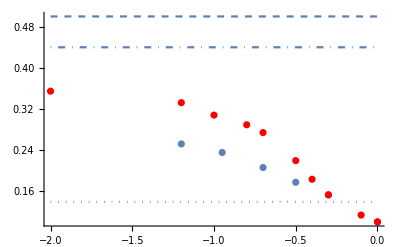

```mathematica
Show[Plot[{x=0.5},{x,-2,0},PlotStyle->Dashed],Plot[{x=0.13913554465063258},{x,-2,0},PlotStyle->Dotted],Plot[{x=0.44},{x,-2,0},PlotStyle->DotDashed],ListPlot[CompacBH],ErrorListPlot[errorCompac, PlotStyle->Red, ErrorBarFunction->Automatic],PlotRange->Automatic]
```

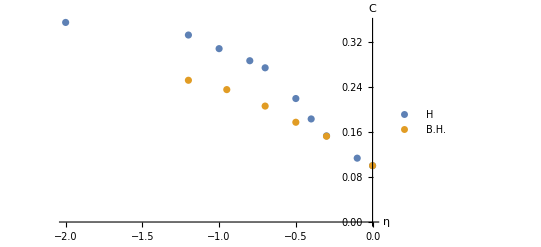

```mathematica
ListPlot[{CompacH,CompacBH},PlotRange->Automatic, AxesLabel->{"η","C"}, PlotLegends->Placed[{"H","B.H."},{0.2,0.25}]]
```